Autor: Krzysztof Barczak

# Metody numeryczne w technice

## (kierunek Matematyka)

## Projekt 6

Metoda sum skończonych

## Równanie Fredholma II rodzaju

### Zadanie

Metodą sum skończonych wyznaczyć rozwiązanie przybliżone równania:

y(x)=7/8 x-1/12+1/4∫_0^1 (x+t) y(t) ⅆt

Wykorzystać metodę trapezów.

Argument:  n

Wyznaczyć rozwiązanie dla n = 2, 4, 6, 8. 
Wykreślić błędy uzyskanych rozwiązań przybliżonych, gdy wiadomo, że rozwiązaniem dokładnym jest funkcja y(x)=x.

### Kod procedury

Procedura realizuje Metodę sum skończonych dla równań postaci: y(x)==f(x)+λ∫_a^b K(x,t)y(t)dt.
Wejście:
	f - zadana funkcja f(x);
	λ - zadana liczba;
	Ker - jądro równania K(x,t);
	a, b - granice całkowania;
	n - zadana liczba naturalna;
	z - argument zwracanej funkcji.
Wyjście:
	Rozwiązanie przybliżone.

```mathematica
Clear[mss];
mss[f_,λ_,Ker_,a_,b_,n_,z_Symbol]:=Module[{h=(b-a)/n,tj,A,Kij,fi,BLambda,yi,y},
tj=Table[a+(j-1)h,{j,n+1}];
A=Table[h,{n-1}];
A=Prepend[Append[A,h/2],h/2];
Kij=Table[Ker[tj[[i]],tj[[j]]],{i,n+1},{j,n+1}];
fi=Table[f[tj[[i]]],{i,n+1}];
BLambda=Table[i,j-λ A⟦j⟧ Kij⟦i,j⟧,{i,n+1},{j,n+1}];
yi=LinearSolve[BLambda,fi];
y[z]:=f[z]+λ ∑_(j=1)^(n+1) A⟦j⟧ Ker[z,tj⟦j⟧] yi⟦j⟧;
Return[Simplify[y[z]]]
]
```

### Rozwiązanie

```mathematica
Clear[f,λ,Ker,a,b];
f[x_]:=(7 x)/8-1/12;λ=1/4;Ker[x_,t_]:=x+t;
a=0;b=1;
rozwiazanie=Table[mss[f,λ,Ker,a,b,n,z],{n,2,8,2}];
rozwiazanie//MatrixForm
```

(1/570 (7+572 z)
(7+2288 z)/2286
(7+5148 z)/5146
(7+9152 z)/9150)

```mathematica
dokladne[x_]:=x;
bledy=Table[{a+1/(2n) (i-1) (b-a),Abs[(rozwiazanie⟦n⟧/.{z->a+1/(2n) (i-1) (b-a)})-dokladne[a+1/(2n) (i-1) (b-a)]]},{n,4},{i,2n+1}];
```

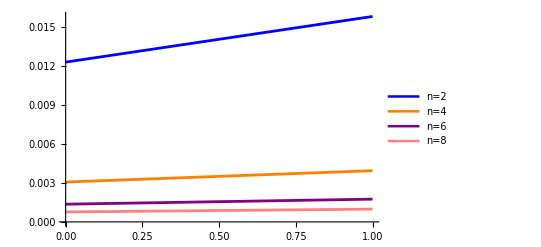

```mathematica
M=Max[bledy[[All,All,2]]];
wykres2=ListPlot[bledy[[1]],Joined->True,PlotLegends->{"n=2"},PlotStyle->{Blue,Thickness[0.005]},PlotRange->{0,M}];
wykres4=ListPlot[bledy[[2]],Joined->True,PlotLegends->{"n=4"},PlotStyle->{Orange,Thickness[0.005]}];
wykres6=ListPlot[bledy[[3]],Joined->True,PlotLegends->{"n=6"},PlotStyle->{Purple,Thickness[0.005]}];
wykres8=ListPlot[bledy[[4]],Joined->True,PlotLegends->{"n=8"},PlotStyle->{Pink,Thickness[0.005]}];
Show[wykres2,wykres4,wykres6,wykres8]
```